```mathematica
Ejercicio. 5.3.
Considera la curva en R dada por las ecuaciones paramétricas:
x = 2cos(t), y = sen(t),
donde t es el parámetro.

(1) Determina la ecuación implícita que define esta curva.
```

```mathematica
Reduce[y-Sin[t]==0,t]
```

C[1]∈Integers&&(t==π-ArcSin[y]+2 π C[1]||t==ArcSin[y]+2 π C[1])

```mathematica
Reduce[x-2Cos[t]==0,t]
```

C[1]∈Integers&&(t==-ArcCos[x/2]+2 π C[1]||t==ArcCos[x/2]+2 π C[1])

```mathematica
Aunque en este caso se puede ver que x^2/4 + y^2 = 1 que viene de elevar al cuadrado y usar la igualdad trigonometrica basica, verifica nuestras ecuaciones, asique operamos con esa


(2) Dibuja esta curva mediante la orden de Mathematica “ParametricPlot”.
```

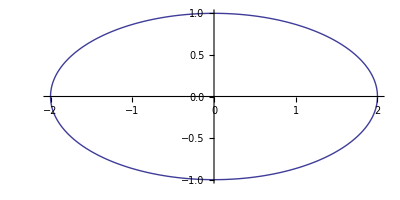

```mathematica
ParametricPlot[{2*Cos[u],Sin[ u]},{u,0,2 Pi}]
```

```mathematica
(3) Dibuja la curva, dada por la ecuación implícita, mediante la orden de Mathematica “ContourPlot”.
Podemos hacer variaciones sobre este ejercicio. Por ejemplo, para cada a ∈ N consideramos la curva
con ecuaciones paramétricas (2cos(t),sen(a t)); el caso a = 1 es el ya estudiado de la elipse; el caso
a = 2 es la Lemniscata de Gerono, etc. Estudiar el caso a = 3.
Compara las ecuaciones implícitas obtenidas en cada uno de los casos, a = 1, 2, 3.
```

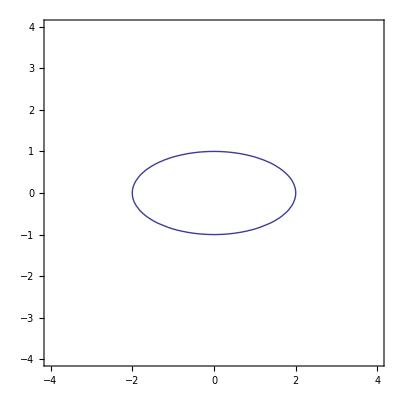

```mathematica
ContourPlot[ x^2/4+y^2==1 ,{x,-4,4},{y,-4,4}]
```

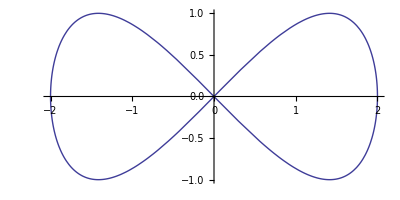

```mathematica
ParametricPlot[{2*Cos[u],Sin[ 2*u]},{u,0,2 Pi}]
```

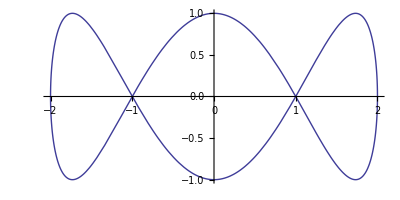

```mathematica
ParametricPlot[{2*Cos[u],Sin[ 3*u]},{u,0,2 Pi}]
```

```mathematica
en cada caso las ecuaciones obtenidas corresponde a la forma
ArcSin[y]/a = ArCos[x]/2 siendo a el parametro buscado
```